```mathematica
t=Import["~/Desktop/bcs-3.csv"]
bc=Table[{i/65536,Log[t[[i,1]]]},{i,2,Length[t],1}];
```

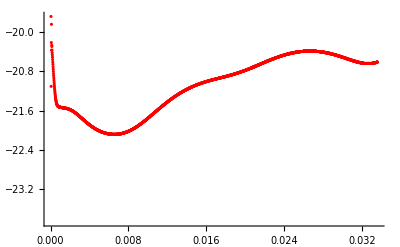

```mathematica
plot1=ListPlot[bc,PlotStyle->Red]
```

```mathematica
t=Import["~/Desktop/bcs-4.csv"]
bc=Table[{i/65536,Log[t[[i,1]]]},{i,2,Length[t],1}];
```

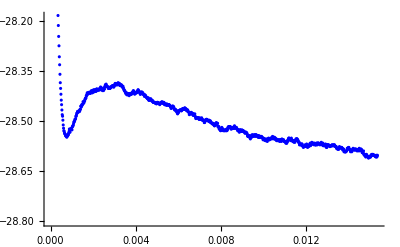

```mathematica
plot2=ListPlot[bc,PlotStyle->Blue]
```

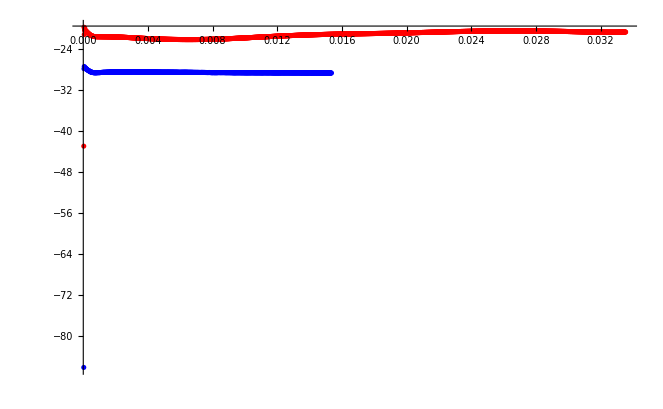

```mathematica
Show[plot1,plot2,PlotRange->Full]
```